The goal of this file is to provide a model independent CANNEX code, where the field can be simulated by simply specifiying the effective potential, the potential minimum, and the mass of the field.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
Needs["MaTeX`"]
flim=Import["cannex_sensitivity_curves.csv"][[1;;]];
PressSen=Interpolation[flim[[All,1;;2]]]; (*Function of d in meters, output in N/m^2*)
PressGradSen=Interpolation[flim[[All,1;;3;;2]]]; (*Function of d in meters, output in N/m^3*)

ρV:=2.28274430389522856994287368414079199874719885301117239489836208132800265957484953105449676513671875`1000.*^-20; (*Define vacuum density*)
ρM=SetPrecision[2514.0*kgm32MeV4,5 CPrec]; 
(*Define mirror density*)
```

## Define mesh, plate separation

434

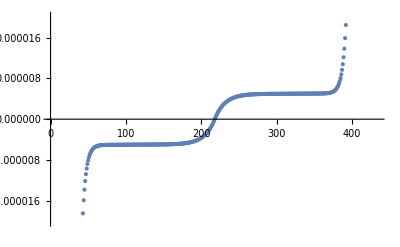

```mathematica
(*All manual definitions have to be made here*)

Clear[dd,nMaxRes,npts1,npts2,cutoff]
Clear[ SOLUTION,Vectorform,λ,A2,β,Prec,MAX,CPrec]
CPrec=500; (*you should not change this value*)

dd=SetPrecision[10*10^-6,5 CPrec]; (* plate separation, has to be in meters *)
nMaxRes=10^4;(*max. resolution in the, this means the smallest distance is dd/nMaxRes*)
npts1=80;(*points in free vacuum and free material, 400*)
npts2=80;(*points in the half-gap, 500*)
nFinePoints=30;(*this amount of points is placed next to the surfaces with minimum resolution*)
minMeshSize=SetPrecision[(dd/nMaxRes),5 CPrec];
cutoff=SetPrecision[0.1,1000]; (*Cutoff for boundary condition inside mirror*)
(*END OF MANUAL DEFINITIONS*)

coordlist[dmin_,ddelta_,dfactor_,nmin_,nmax_]:=Block[{i,dummy},
dummy=Table[N[dmin,5 CPrec],nmax-nmin+1];
If[nmin==0,
For[i=1,i<=nmax,i++,
dummy[[i+1]]=dummy[[i]]+N[ddelta*dfactor^i,5 CPrec];
];,
dummy[[1]]+=Sum[N[ddelta*dfactor^i,5 CPrec],{i,1,nmin}];
For[i=2,i<=nmax-nmin+1,i++,
dummy[[i]]=dummy[[i-1]]+N[ddelta*dfactor^(nmin+i-1),5 CPrec];
];];
N[dummy,5 CPrec]
];

m=m2invMeV;

Clear[rho,ρ];
rho[z_]:=SetPrecision[Piecewise[{{ρV,(-0.5*dd<z<0.5*dd)},{ρM,z≤-0.5*dd||z>=0.5*dd}}],5CPrec];
ρ[z_]:=rho[z]

dist1=SetPrecision[cutoff,5CPrec];(* from -∞ to the border of the lower plate*)

minMeshSize=SetPrecision[(dd/nMaxRes),5 CPrec];

f1=(*von -π/2 bis -dd/2*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[dist1-dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

f4=(*half gab between plates*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts2-1}],5 CPrec]==SetPrecision[dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.001},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

points=SetPrecision[Sort[N[Join[
(* lower plate *)
coordlist[N[-nFinePoints*minMeshSize-dd/2,5 CPrec],-minMeshSize,f1,1,npts1-1],
Table[N[-i*minMeshSize-dd/2,5 CPrec],{i,0,nFinePoints-1}],
Table[N[i*minMeshSize-dd/2,5 CPrec],{i,1,nFinePoints}],
(*Table[-cutoff+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}] ,*)
(*in between plates*)
coordlist[N[nFinePoints*minMeshSize-dd/2,5 CPrec],minMeshSize,f4,1,npts2-2],coordlist[dd/2-N[nFinePoints*minMeshSize,5 CPrec],-minMeshSize,f4,1,npts2-1],
Table[dd/2-N[i*minMeshSize,5 CPrec],{i,0,nFinePoints-1}](* inter-spacing *),
Table[dd/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints-1}],

(* upper plate *)
coordlist[N[nFinePoints*minMeshSize+dd/2,5 CPrec],minMeshSize,f1,1,npts1-1](*,
Table[cutoff-N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}]*)

]]](*free space from right*),5CPrec];
points[[1]]=-SetPrecision[cutoff,1000];
points[[-1]]=SetPrecision[cutoff,1000];

Length[points]

ListPlot[points]
```

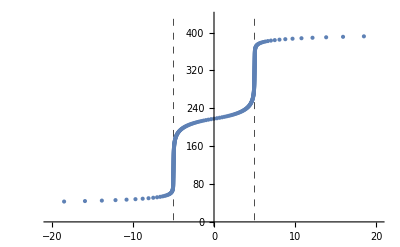

```mathematica
points2={};
For[i=1,i<=Length[points],i++,AppendTo[points2,{10^6 points[[i]],i}]]
grid=ListPlot[points2,LabelStyle->{FontFamily->"Arial",FontSize->13},

AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\text{grid point index}",Magnification->1.2]},GridLinesStyle->Directive[Black,Thick,Dashed],GridLines->{{-5,5},{}}]
```

```mathematica
Export["grid.pdf",grid]
```

grid.pdf

## Example Dilaton field

```mathematica
Clear[ϕρ,Veff,DVeff,DDVeff]
ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<1000000,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3) (6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]

Veff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/(2 mpl^2) ϕ^2,1000]

DVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[-λ/mpl*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ϕ,1000]
DDVeff[ϕ_,A_,λ_,β_,ρ_] :=   SetPrecision[λ^2/mpl^2*ⅇ^SetPrecision[-λ ϕ/mpl+β/Log10[E],1000] + (A ρ)/mpl^2 ,1000]
```

{50.9219,Null}

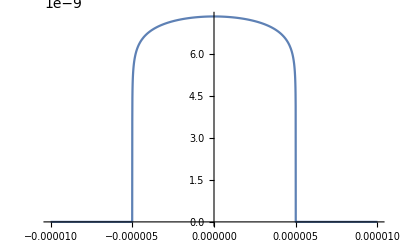

```mathematica
Clear[CPrec,FINAL,A2,β,λ,SEED,Guess2]
CPrec=15;(*this defines the precision used for the newtons method, can be arbitrarily high*)
λ=SetPrecision[10^(31),1000];
A2=10^45;
β=10^0;

Clear[ρV,rhoV]
ρV=0;
rhoV=ρV;

Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[A2,λ,β,ρM]]]]

Prec=100;
MAX=100;

Timing[{Vectorform,SOLUTION}=SOLVEFD[A2,λ,β,points,Prec,MAX,Seed,DVeff,DDVeff];]

(*Print["If > 1 excluded"]
Abs[Pressure[A2,λ,β,DVeff,DDVeff]/SetPrecision[PressSen[dd],10]]*)

Plot[SOLUTION[z]-ϕρ[A2,λ,β,ρM],{z,-dd,dd},WorkingPrecision->100]
```

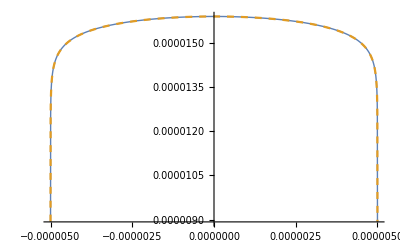

```mathematica
Plot[{SOLUTION[z],ϕ[z*m2invMeV,λ,A2,β,ϕ00]},{z,-dd/2,dd/2},WorkingPrecision->100,PlotStyle->{Thick,Dashed},PlotRange->Full]
```

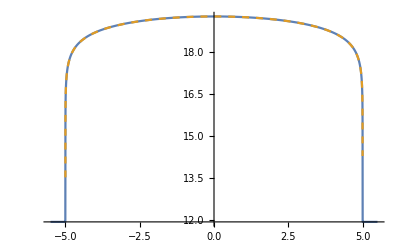

```mathematica
δ=SetPrecision[10^-10,1000];
COMP1=Plot[{SOLUTION[z*10^-6]*10^9,ϕ[z*m2invMeV*10^-6,λ,A2,β,ϕ00]*10^9},{z,-1.1*5,1.1*5},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]},PlotStyle->{Thick,Dashed},PlotLegends->Placed[Grid[{{LineLegend[{ColorData[97][1]},{MaTeX["\\text{numerical solution}",Magnification->1.2]}],LineLegend[{ColorData[97][2]},{MaTeX["\\text{analytical solution}",Magnification->1.2]}]}}],Below],Exclusions->None]
```

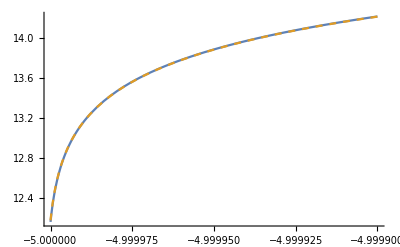

```mathematica
δ=SetPrecision[1*10^-4,1000];
COMP2=Plot[{SOLUTION[z*10^-6]*10^9,ϕ[z*m2invMeV*10^-6,λ,A2,β,ϕ00]*10^9},{z,-5,-5+δ},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]},PlotStyle->{Thick,Dashed},PlotLegends->Placed[Grid[{{LineLegend[{ColorData[97][1]},{MaTeX["\\text{numerical solution}",Magnification->1.2]}],LineLegend[{ColorData[97][2]},{MaTeX["\\text{analytical solution}",Magnification->1.2]}]}}],Below],Exclusions->None]
```

```mathematica
Export["COMP1.pdf",COMP1]
Export["COMP2.pdf",COMP2]
```

COMP1.pdf

COMP2.pdf

## Example Symmetron field

```mathematica
Clear[ϕρ,Veff,DVeff,DDVeff]

ϕρ[μ_,λ_, M_,ρ_]:=If[μ^2/λ-ρ/(M^2 λ)>0,Sqrt[SetPrecision[μ^2/λ-ρ/(M^2 λ),5CPrec]],0]

Veff[ϕ_,μ_,λ_, M_,ρ_]:=SetPrecision[1/2 (ρ/M^2-μ^2)ϕ^2+λ/4 ϕ^4,5CPrec]

DVeff[ϕ_,μ_,λ_, M_,ρ_] :=   SetPrecision[(ρ/M^2-μ^2)ϕ+λ ϕ^3,5CPrec]
DDVeff[ϕ_,μ_,λ_, M_,ρ_] :=   SetPrecision[(ρ/M^2-μ^2)+3*λ*ϕ^2,5CPrec]

(*The below Approx allows to calculate a Seed based on expanding the effective potential around its density dependent minimum to second order, this works much better
as a seed than the seeds for the dilaton and chameleon models*)
DVeffApprox[ϕ_,μ_,λ_, M_,ρ_] :=  DDVeff[ϕρ[μ,λ, M,ρ],μ,λ, M,ρ]*(ϕ-ϕρ[μ,λ, M,ρ])
DDVeffApprox[ϕ_,μ_,λ_, M_,ρ_] :=   DDVeff[ϕρ[μ,λ, M,ρ],μ,λ, M,ρ]
```

{0.859375,Null}

{4.60938,Null}

If > 1 excluded

0.0005784065066

General::munfl: (-«1045»)/(-1.2731×10^-6) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («1040»)/(2.2417×10^-6) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-«1041»)/(-3.91503×10^-6) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

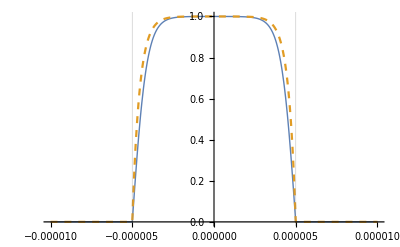

```mathematica
μ=SetPrecision[10^-0.5*10^-6,30];
M=SetPrecision[10^-6.2*10^3,30];
λ=10^3;

Prec=100;
MAX=100;

Timing[{Vectorform,SEED}=SOLVEFD[μ,λ, M,points,Prec,MAX,"Default",DVeffApprox,DDVeffApprox];]
Timing[{Vectorform2,SOLUTION}=SOLVEFD[μ,λ, M,points,Prec,MAX,Vectorform,DVeff,DDVeff];] (*This uses the approximation as seed*)

Print["If > 1 excluded"]
Abs[Pressure[μ,λ, M,DVeff,DDVeff]/SetPrecision[PressSen[dd],10]]

Plot[{(SOLUTION[x]-ϕρ[μ,λ, M,ρM])/(ϕρ[μ,λ, M,ρV]-ϕρ[μ,λ, M,ρM]),(SEED[x]-ϕρ[μ,λ, M,ρM])/(ϕρ[μ,λ, M,ρV]-ϕρ[μ,λ, M,ρM])},{x,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotRange->Full,WorkingPrecision->100,PlotStyle->{Thick,Dashed}]
```

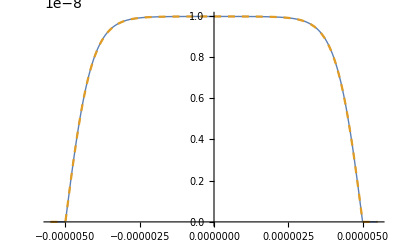

```mathematica
Plot[{SOLUTION[x],SOL[x]},{x,-1.1*dd/2,1.1*dd/2},PlotRange->Full,PlotStyle->{Thick,Dashed}]
```

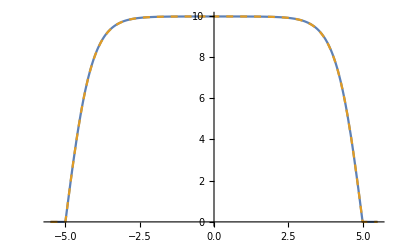

```mathematica
COMP4=Plot[{SOLUTION[z*10^-6]*10^9,SOL[z*10^-6]*10^9},{z,-1.1*5,1.1*5},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]},PlotStyle->{Thick,Dashed},PlotLegends->Placed[Grid[{{LineLegend[{ColorData[97][1]},{MaTeX["\\text{numerical solution}",Magnification->1.2]}],LineLegend[{ColorData[97][2]},{MaTeX["\\text{analytical solution}",Magnification->1.2]}]}}],Below],Exclusions->None]
```

```mathematica
Export["COMP4.pdf",COMP4]
```

COMP4.pdf

## Example Chameleon field

```mathematica
Clear[ϕρ,Veff,DVeff,DDVeff]

ϕρ[Λ_,Mc_,n_,ρ_]:=(SetPrecision[(n*Mc* Λ^SetPrecision[4+n,1000])/ρ,1000])^(1/(n+1))

Veff[ϕ_,Λ_,Mc_,n_,ρ_]:=SetPrecision[(ρ ϕ)/Mc+Λ^SetPrecision[4+n,1000] ϕ^SetPrecision[-n,1000],1000]

DVeff[ϕ_,Λ_,Mc_,n_,ρ_] :=   SetPrecision[ρ/Mc-n*Λ^SetPrecision[4+n,1000] ϕ^SetPrecision[-n-1,1000],1000]
DDVeff[ϕ_,Λ_,Mc_,n_,ρ_] :=  SetPrecision[n*(n+1)*Λ^SetPrecision[4+n,1000] ϕ^SetPrecision[-n-2,1000],1000]
```

{8.45313,Null}

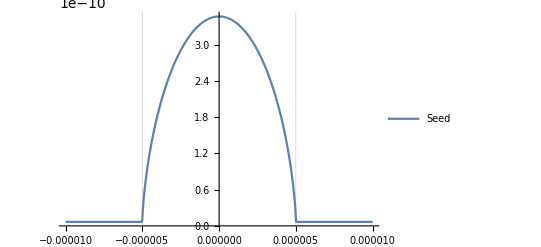

```mathematica
ρV=0;
rhoV=0;


MAX=50;
Prec=15;
n=1;
β=SetPrecision[4.1*10^5,100];
Mc=mpl/β;
Λ=SetPrecision[2.4*10^-6*10^(-3),1000];


Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]]]]

(*Print["If > 1 excluded"]
Abs[Pressure[Λ,Mc,n,DVeff,DDVeff]/SetPrecision[PressSen[dd],10]]*)

Timing[{Vectorform,SOLUTION}=SOLVEFD[Λ,Mc,n,points,Prec,MAX,Seed,DVeff,DDVeff];]

Plot[{SOLUTION[x]},{x,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotLegends->{"Seed","RealSolution"},PlotRange->Full]
```

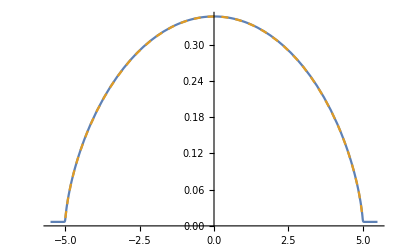

```mathematica
δ=SetPrecision[10^-10,1000];
COMP3=Plot[{SOLUTION[z*10^-6]*10^9,Sol2[z*10^-6]*10^9},{z,-1.1*5,1.1*5},PlotRange->Full,FrameLabel->{Style["x-axis",Bold,12],Style["y-axis",Bold,12]},LabelStyle->{FontFamily->"Arial",FontSize->13},AxesLabel->{MaTeX["z[\\mu m]",Magnification->1.2],MaTeX["\\phi (z)[\\text{meV}]",Magnification->1.2]},PlotStyle->{Thick,Dashed},PlotLegends->Placed[Grid[{{LineLegend[{ColorData[97][1]},{MaTeX["\\text{numerical solution}",Magnification->1.2]}],LineLegend[{ColorData[97][2]},{MaTeX["\\text{analytical solution}",Magnification->1.2]}]}}],Below],Exclusions->None,WorkingPrecision->100]
```

```mathematica
Export["COMP3.pdf",COMP3]
```

COMP3.pdf